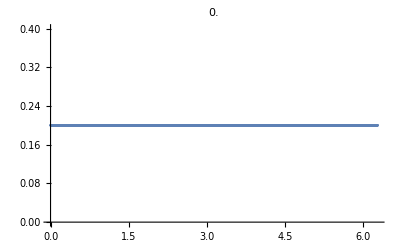
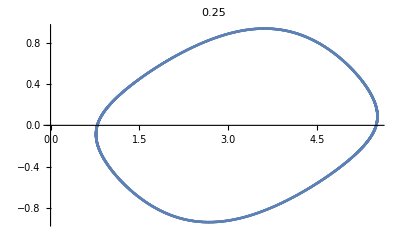
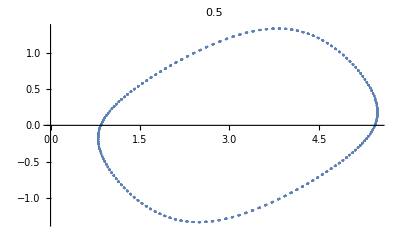
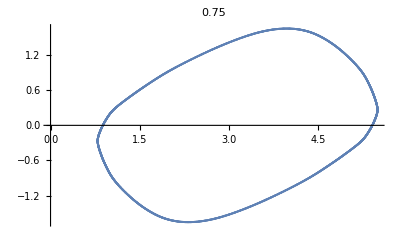
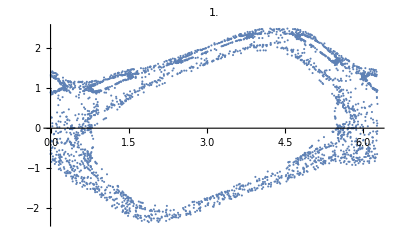
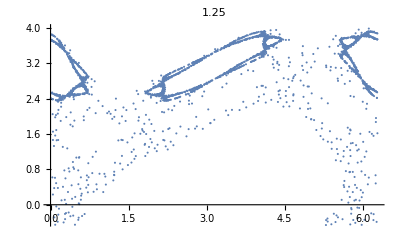
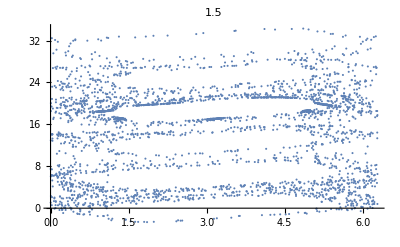
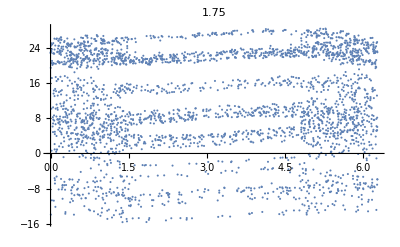

```mathematica
Table[{coor={1,0.2};data=Table[{pnext=1.coor[[2]]+k*Sin[coor[[1]]];qnext=Mod[coor[[1]]+pnext,2Pi];coor={qnext,pnext};qnext,pnext},3000];ListPlot[data,PlotLabel->k]},{k,0,4,0.25}]
```